Try to reproduce the analysis done in the LIGO GW150914 tutorial <https://losc.ligo.org/s/events/GW150914/GW150914_tutorial.html>.

```mathematica
<<SimulationTools`
```

Load the “NR” data from LIGO python tutorial, which is described as: “This NR template corresponds to the signal expected from a pair of black holes with masses of around 36 and 29 solar masses, merging into a single black hole of 62 solar masses, at a distance of around 410 Mpc.”

```mathematica
hLIGO=ToDataTable[Import["~/Research/Projects/GW150914/GW150914_tutorial/GW150914_4_NR_waveform.txt","TABLE"]];
```

This appears to be pretty much (exactly?) the waveform given in Fig. 2 of the LIGO PRL, up to a time shift and multiplication by a factor of 10^21.

```mathematica
hPRL=Shifted[ToDataTable[Import["~/Research/Projects/GW150914/GW150914sim/Analysis/fig2-unfiltered-waveform-H.txt","TABLE"][[2;;]]],-0.4227];
```

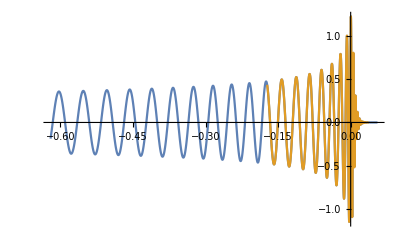

```mathematica
ListLinePlot[{10^21 hLIGO,hPRL}]
```

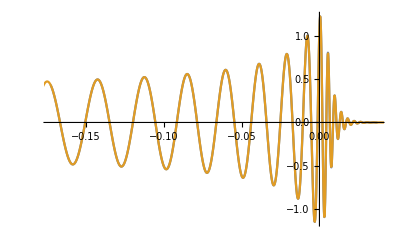

```mathematica
ListLinePlot[{hPRL,10^21 hLIGO},PlotRange->{CoordinateRange[hPRL],All}]
```

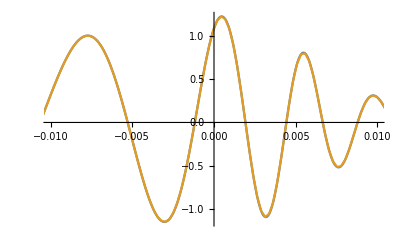

```mathematica
Show[%,PlotRange->{{-0.01,0.01},All}]
```

SpEC data from SXS:BBH:0305

```mathematica
tSpEC=Import["~/Research/Projects/GW150914/GW150914sim/Analysis/rhOverM_Asymptotic_GeometricUnits.h5",{"Datasets","Extrapolated_N2.dir/Y_l2_m-2.dat"}][[All,1]];
```

```mathematica
Do[hSpEC[l,m]=Complex@@@Import["~/Research/Projects/GW150914/GW150914sim/Analysis/rhOverM_Asymptotic_GeometricUnits.h5",{"Datasets","Extrapolated_N2.dir/Y_l"<>ToString[l]<>"_m"<>ToString[m]<>".dat"}][[All,{2,3}]];,{l,2,8},{m,-l,l}];
```

Convert time coordinate to seconds, accounting for redshift (0.09) and units for a binary with total mass of (36+29)M_☉. This isn’t quite consistent with SXS:BBH:0305, which appears to have mass ratio 11:9, but it’s the total mass that is most important to get right.

```mathematica
z=0.09;
```

```mathematica
Mtot=(1+z)(36+29)SolarMassInSeconds;
```

```mathematica
Do[h[l,m]=ToDataTable[tSpEC Mtot,hSpEC[l,m]];,{l,2,8},{m,-l,l}]
```

Also consider another configuration with source-frame mass of 68.5 M_☉.

```mathematica
Do[hAlt[l,m]=ToDataTable[tSpEC (1+z)68.5SolarMassInSeconds,hSpEC[l,m]];,{l,2,8},{m,-l,l}]
```

Shift so that the merger is at t=0

```mathematica
tMerger=LocateMaximum[Abs[h[2,2]]];
```

```mathematica
Do[h[l,m]=Shifted[h[l,m],-tMerger],{l,2,8},{m,-l,l}];
```

```mathematica
tMergerAlt=LocateMaximum[Abs[hAlt[2,2]]];
```

```mathematica
Do[hAlt[l,m]=Shifted[hAlt[l,m],-tMergerAlt],{l,2,8},{m,-l,l}];
```

Check that the 2,2 mode dominates, even at merger

```mathematica
Sort[Flatten[Table[{l,m,Interpolation[Abs[h[l,m]],0]},{l,2,8},{m,-l,l}],1],#1[[3]]>#2[[3]]&]
```

{{2,-2,0.389458},{2,2,0.389458},{3,-3,0.0218232},{3,3,0.0218231},{4,-4,0.0216675},{4,4,0.0216674},{3,2,0.0154609},{3,-2,0.015458},{2,1,0.0111398},{2,-1,0.0111398},{2,0,0.0105407},{5,-5,0.00334995},{5,5,0.00334993},{6,-6,0.00210816},{6,6,0.00210815},{3,0,0.00169692},{5,4,0.00132083},{5,-4,0.00132039},{4,3,0.00106868},{4,-3,0.00106818},{3,1,0.000535741},{3,-1,0.000535592},{7,-7,0.00051283},{7,7,0.000512828},{4,-2,0.000426232},{4,2,0.00042595},{8,-8,0.000255744},{8,8,0.000255742},{6,5,0.000190285},{6,-5,0.00019016},{7,6,0.000153264},{7,-6,0.000153196},{4,-1,0.0000723152},{4,1,0.000072313},{5,3,0.0000712956},{5,-3,0.0000712749},{6,-4,0.0000558716},{6,4,0.0000558263},{5,2,0.0000402239},{5,-2,0.0000402173},{8,7,0.0000339514},{8,-7,0.0000339277},{4,0,0.0000128168},{7,-5,9.83483×10^-6},{7,5,9.83322×10^-6},{6,-3,8.73988×10^-6},{6,3,8.73912×10^-6},{8,-6,6.45306×10^-6},{8,6,6.44525×10^-6},{6,2,6.05999×10^-6},{6,-2,6.05948×10^-6},{5,0,5.74762×10^-6},{7,4,5.30497×10^-6},{7,-4,5.30288×10^-6},{5,1,2.45688×10^-6},{5,-1,2.45606×10^-6},{8,5,1.44788×10^-6},{8,-5,1.44751×10^-6},{6,-1,1.01905×10^-6},{6,1,1.01897×10^-6},{7,3,8.20508×10^-7},{7,-3,8.20202×10^-7},{8,4,6.54621×10^-7},{8,-4,6.54358×10^-7},{7,0,5.67562×10^-7},{7,2,1.54286×10^-7},{7,-2,1.54247×10^-7},{8,0,8.72913×10^-8},{8,-2,6.98305×10^-8},{8,2,6.98183×10^-8},{7,-1,5.11352×10^-8},{7,1,5.11352×10^-8},{8,3,4.831×10^-8},{8,-3,4.80741×10^-8},{6,0,4.28807×10^-8},{8,1,2.59215×10^-8},{8,-1,2.58543×10^-8}}

Now compare to the LIGO tutorial waveform, allowing for arbitrary magnitude and phase factors

```mathematica
Manipulate[ListLinePlot[{hLIGO,Re[a Exp[I ϕ]h[2,2]],Re[a Exp[I ϕ]hAlt[2,2]]},PlotRange->{{-0.65,0.05},All},ImageSize->800],{{a,3.039 10^-21},2.5 10^-21,3.5 10^-21},{{ϕ,4.1846},0,2π}]
```